```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

## Are first terms in kappa and Maxwellian n-V relations comparable?

```mathematica
Tm=100;
```

```mathematica
firstKappaTerm[pot_Real,Tm_Real,nm_Real,kappa_Real]:=nm *(pot/Tm)^(3/2)/Sqrt[π] Gamma[kappa+1]/((kappa-3/2)^(3/2) Gamma[kappa-1/2])NIntegrate[Sqrt[Ebar+1] (1+(Ebar (pot/Tm))/(kappa-3/2))^-(kappa+1),{Ebar,0,∞}]
```

```mathematica
firstKappaTermModdedV2[pot_Real,Tm_Real,nm_Real,kappa_Real]:=nm *(pot/Tm)^(3/2)/Sqrt[π] Gamma[kappa+1]/((kappa-3/2)^(3/2) Gamma[kappa-1/2])NIntegrate[Sqrt[Ebar+1] (1+(Ebar (pot/Tm))/(kappa-3/2))^-(kappa+1),{Ebar,0,1}]
```

```mathematica
firstKappaTermModded[pot_Real,Tm_Real,nm_Real,kappa_Real]:=nm *(pot/Tm)^(3/2)/Sqrt[π] Gamma[kappa+1]/((kappa-3/2)^(3/2) Gamma[kappa-1/2])(NIntegrate[Sqrt[Ebar+1] (1+(Ebar (pot/Tm))/(kappa-3/2))^-(kappa+1),{Ebar,0,∞}]-Tm(1-3/(2kappa))/pot)
```

```mathematica
firstMaxwellianTerm[pot_Real,Tm_Real,nm_Real]:=nm*1/2 *Exp[pot/Tm] Erfc[Sqrt[pot/Tm]]
```

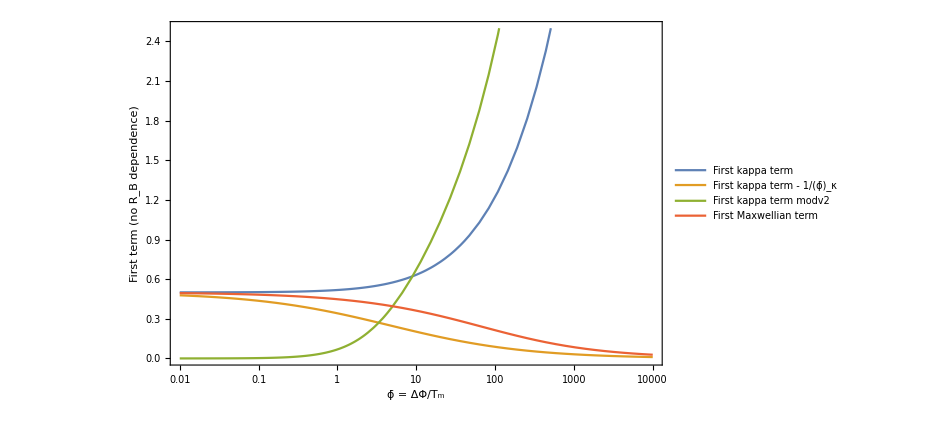

```mathematica
LogLinearPlot[{firstKappaTerm[pot,Tm,1,180/100],firstKappaTermModded[pot,Tm,1,155/100],firstKappaTermModdedV2[pot,Tm,1,155/100],firstMaxwellianTerm[pot,Tm,1]},{pot,0.01,10000},PlotRange->{All,{0.0,2.5}},PlotLegends->{"First kappa term","First kappa term - 1/(ϕ̄)_κ","First kappa term modv2","First Maxwellian term"},Frame->True,FrameLabel->{"ϕ̄ = ΔΦ/T_m","First term (no R_B dependence)"},ImageSize->700,LabelStyle->(FontSize->22)]
```

```mathematica
nVMaxwellian[10,1.01,100,1]//N
```

0.371252

## Exact second kappa term, with a=ϕ^__/(R_B-1)

```mathematica
Integrate[√(1-y/a)(1+y/(kappa-3/2))^(-1-kappa),{y,0,a}]
```

ConditionalExpression[(2 a (-3+2 kappa) Hypergeometric2F1[1,3/2-kappa,5/2,(2 a)/(-3+2 a+2 kappa)])/(-9+6 a+6 kappa),Re[(3-2 kappa)/a]>2||Re[(3-2 kappa)/a]<0||(3-2 kappa)/a∉ℝ]

## Trying to do small-RB expansion. (Full job done in "R_B limits for n-V relations" pages, dated 2018/08/21)

```mathematica
this=Normal@Series[1/(1-x),{x,0,10}]
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10

```mathematica
RBthing=Simplify@(-1/RB(this/.x->1/RB))
```

-(1+RB+RB^2+RB^3+RB^4+RB^5+RB^6+RB^7+RB^8+RB^9+RB^10)/RB^11

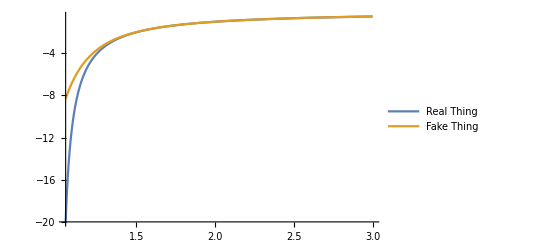

```mathematica
Plot[{-1/(RB-1),RBthing},{RB,1.05,3},PlotRange->Full,PlotLegends->{"Real Thing","Fake Thing"}]
```

```mathematica
Integrate[√(1-x)x^(-1-κ),{x,0,1},Assumptions->κ>3/2]
```

Integrate::idiv: Integral of √(1-x) x^(-1-κ) does not converge on {0,1}.

Integrate[√(1-x) x^(-1-κ),{x,0,1},Assumptions→κ>3/2]